```mathematica
ct =(gamma (pCM ctCM + ß ECM))/((gamma^2(ECM +ß pCM ctCM)^2-mN^2)^(1/2));
getCosTheta[ctCM_]:=Evaluate[ct]
```

```mathematica
myctCM = Solve[(gamma (pCM ctCM + ß ECM))/((gamma^2(ECM +ß pCM ctCM)^2-mN^2)^(1/2))-ctLAB ==0,{ctCM}]//FullSimplify
```

{{ctCM→-(√(ctLAB^2 gamma^2 pCM^2 (mN^2 (ctLAB^2 ß^2-1)+ECM^2 gamma^2 (ß^2-1)^2))+(ctLAB^2-1) ECM gamma^2 pCM ß)/(gamma^2 pCM^2 (ctLAB^2 ß^2-1))},{ctCM→(√(ctLAB^2 gamma^2 pCM^2 (mN^2 (ctLAB^2 ß^2-1)+ECM^2 gamma^2 (ß^2-1)^2))-(ctLAB^2-1) ECM gamma^2 pCM ß)/(gamma^2 pCM^2 (ctLAB^2 ß^2-1))}}

```mathematica
Kallen[a_,b_,c_]:= (a-b-c)^2-4b*c
```

```mathematica
subBeta={ß-> √(1-1/gamma^2)};
subECM ={ECM->(mK^2+mN^2-ml^2)/(2 mK)};subpCM={pCM-> mK/2*√Kallen[1,(mN/mK)^2,(ml/mK)^2]};
```

```mathematica
cosTCMmin = Solve[(getCosTheta'[T]//FullSimplify//PowerExpand//FullSimplify)==0,T]/.subBeta/.subECM/.subpCM//FullSimplify//PowerExpand//FullSimplify
```

{{T→-(√(mK-ml-mN) √(mK+ml-mN) √(mK-ml+mN) √(mK+ml+mN))/(√(1-1/gamma^2) (mK^2-ml^2+mN^2))}}

```mathematica
(getCosTheta[T]/.cosTCMmin/.subBeta/.subECM/.subpCM//Simplify//PowerExpand//Simplify)/.{mK-> Kaonmass,ml-> Muonmass,mN-> 0.1, gamma-> 1.1}
```

{0.+4.77548 ⅈ}

```mathematica
simpctCM=ctCM/.myctCM[[1]]/.subBeta/.subECM/.subpCM//FullSimplify//PowerExpand//FullSimplify
simpctCMm=ctCM/.myctCM[[2]]/.subBeta/.subECM/.subpCM//FullSimplify//PowerExpand//FullSimplify
```

(ctLAB (-√(-2 mK^2 (mN^2 (-2 ctLAB^2 (gamma^2-1)+2 gamma^2-1)+ml^2)+mK^4+(ml^2-mN^2)^2))-(ctLAB^2-1) gamma √(gamma^2-1) (mK^2-ml^2+mN^2))/((ctLAB^2 (gamma^2-1)-gamma^2) √(mK-ml-mN) √(mK+ml-mN) √(mK-ml+mN) √(mK+ml+mN))

(ctLAB √(-2 mK^2 (mN^2 (-2 ctLAB^2 (gamma^2-1)+2 gamma^2-1)+ml^2)+mK^4+(ml^2-mN^2)^2)-(ctLAB^2-1) gamma √(gamma^2-1) (mK^2-ml^2+mN^2))/((ctLAB^2 (gamma^2-1)-gamma^2) √(mK-ml-mN) √(mK+ml-mN) √(mK-ml+mN) √(mK+ml+mN))

```mathematica
getCosThetaCM[x_]:=Evaluate[(simpctCM/.ctLAB-> x)]//FullSimplify//PowerExpand//FullSimplify
getCosThetaCMm[x_]:=Evaluate[(simpctCM/.ctLAB-> x)]//FullSimplify//PowerExpand//FullSimplify
```

```mathematica
ctMAX[mN_,mK_,ml_,gamma_]:=Evaluate[ct/.ctCM-> 1/.subBeta/.subECM/.subpCM]
ctMIN[mN_,mK_,ml_,gamma_]:=Evaluate[ct/.ctCM-> -1/.subBeta/.subECM/.subpCM]
```

```mathematica
Kaonmass=0.495;Muonmass=0.112;
Ratio[mN_,mK_,ml_,gamma_]:=Evaluate[((getCosThetaCM[1]-getCosThetaCM[0])/(getCosThetaCM[1]-getCosThetaCM[0]/.mN-> 0))]
cTCM0[mN_,mK_,ml_,gamma_,CT_]:=Evaluate[getCosThetaCM[CT]//Simplify]
cTCM0m[mN_,mK_,ml_,gamma_,CT_]:=Evaluate[getCosThetaCMm[CT]//Simplify]
```

```mathematica
ctMIN[0.03,Kaonmass,Muonmass,10]
```

1.

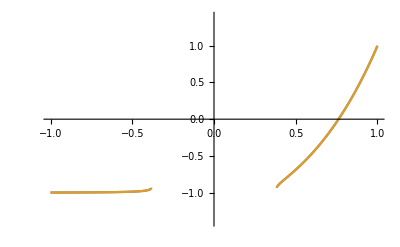

```mathematica
Plot[{cTCM0[0.3,Kaonmass,Muonmass,1.1,x],cTCM0m[0.3,Kaonmass,Muonmass,1.1,x]},{x,-1,1},PlotRange->{{-1,1},{-1.4,1.4}},PlotPoints->10000]
```

```mathematica
Plot[{cTCM0[0.3,Kaonmass,Muonmass,1.1,x],cTCM0m[0.3,Kaonmass,Muonmass,1.1,x]},{x,-1,1},PlotRange->{{-1,1},{-1.4,1.4}},PlotPoints->10000]
```

-Graphics-

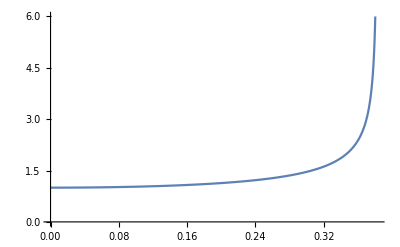

```mathematica
Plot[Ratio[x,Kaonmass,Muonmass,1.1],{x,0,Kaonmass-Muonmass},PlotRange->{{0,Kaonmass-Muonmass},{0,6}}]
```